```mathematica
Needs["PlotLegends`"]
```

```mathematica
SetOptions[{ListPlot,ListLogPlot,ListLogLogPlot},BaseStyle->{FontFamily->"Helvetica", 14},ImageSize-> 600,Joined-> True,PlotStyle-> Thick,
Axes-> False,Frame-> True];
SetOptions[{ Plot, LogPlot, LogLogPlot},BaseStyle->{FontFamily->"Helvetica", 14},ImageSize-> 600,PlotStyle-> Thick,
Axes-> False,Frame-> True];
```

```mathematica
z=I .8;
y=I 5 10^-6;
zc=Sqrt[z/y];
γ=Sqrt[z y];
```

```mathematica
Q[θ_]:={{Cosh[θ ], zc Sinh[θ ]},{1/zc  Sinh[θ ], Cosh[θ]}}
```

```mathematica
a=Q[I θ][[1,1]];
b=Q[I θ][[1,2]];
```

```mathematica
pc=1/zc
```

0.0025

```mathematica
pr[θ_]=1/Abs[b] Cos[Arg[b]-δ]+Abs[a/b] Cos[Arg[b]-δ];
```

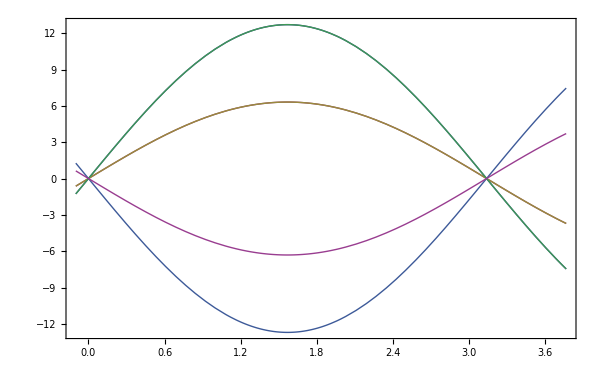

```mathematica
Plot[{pr[0.05 π]/pc,pr[.1 π]/pc,pr[.9 π ]/pc,pr[.95 π ]/pc,pr[1.05 π]/pc,pr[1.1 π]/pc },{δ,-.10,1.2  π},PlotLegend->{"a","b","c","d", "e","f"},LegendPosition->{1.1,-0.4},LegendShadow->{.0,0}, LegendSize->1.]
```

```mathematica
fun=Cos[90 Degree-δ]/Sin[θ]/.θ-> {0.05 π, .1 π, .9 π, .95 π, 1.05 π, 1.1 π}
```

{6.39245 Sin[δ],3.23607 Sin[δ],3.23607 Sin[δ],6.39245 Sin[δ],-6.39245 Sin[δ],-3.23607 Sin[δ]}

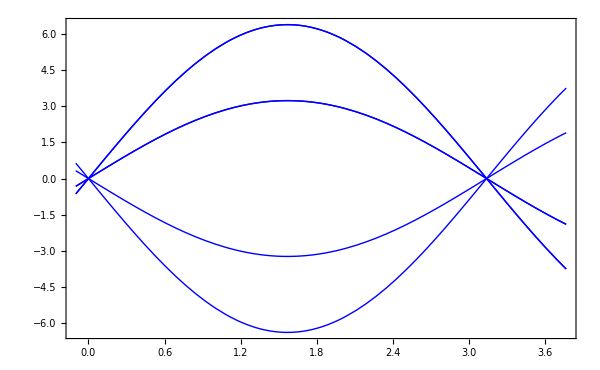

```mathematica
Plot[Cos[90 Degree-δ]/Sin[θ]/.θ-> {0.05 π, .1 π, .9 π, .95 π, 1.05 π, 1.1 π},{δ,-.10,1.2  π},PlotStyle->{Thick,Blue}]
```